# Approximations to the PrimePi Function

The PrimePi function(π[x]) shows the number of primes that are smaller than certain value x. Throughout history, there has been several approximation models of Prime-Counting function(π[x]). These models are important in that they reveal the long-term distribution of prime numbers (Prime Number Theorem, PNT) and help study various mathematical concepts such as LogIntegral and Big-O.

## Distribution of Prime Numbers

Let’s first look at the simple characteristic of prime numbers.

Make a list of divisors for numbers from 2 to 10:

```mathematica
Table[Divisors[n],{n,2,10}]
```

{{1,2},{1,3},{1,2,4},{1,5},{1,2,3,6},{1,7},{1,2,4,8},{1,3,9},{1,2,5,10}}

Prime numbers are the ones that only have trivial divisors (i.e. 1 and itself). Thus, prime numbers have only 2 divisors.

Select a list of divisors with length 2 for numbers from 2 to 10:

```mathematica
Select[Table[Divisors[n],{n,2,10}],Length[Level[#,1]]==2&]
```

{{1,2},{1,3},{1,5},{1,7}}

Now let’s find the number of primes that are smaller than 100.

Select prime numbers that are less than 100:

```mathematica
Select[Table[Prime[n],{n,100}],#<100&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

Here is the number of primes that are less than 100:

```mathematica
Length[Select[Table[Prime[n],{n,100}],#<100&]]
```

25

Let’s now look at the distribution of primes by looking at the number of primes that are smaller than 10^k.

Make a table of values with columns 10^k, number of primes smaller than 10^k, and frequency of primes under 10^k:

```mathematica
Grid[Table[{n,PrimePi[n],Round[PrimePi[n]/n,0.001]},{n,Table[10^k,{k,2,14}]}],Alignment ->  Left]
```

100 | 25 | 0.25
1000 | 168 | 0.168
10000 | 1229 | 0.123
100000 | 9592 | 0.096
1000000 | 78498 | 0.078
10000000 | 664579 | 0.066
100000000 | 5761455 | 0.058
1000000000 | 50847534 | 0.051
10000000000 | 455052511 | 0.046
100000000000 | 4118054813 | 0.041
1000000000000 | 37607912018 | 0.038
10000000000000 | 346065536839 | 0.035
100000000000000 | 3204941750802 | 0.032

To see the distribution of prime numbers, let’s look at how the number of primes change with respect to positive integer n.

Make a plot of PrimePi function:

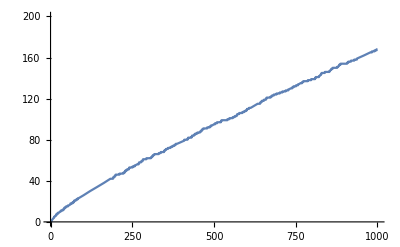

```mathematica
Plot[PrimePi[n],{n,0,1000},PlotRange-> {0,200}]
```

## First Approximation to the PrimePi Function

Looking at how PrimePi function changes with n, let’s now find out the general pattern which the function contains. Lets look and the ratio of n to PrimePi[n].

Make a table of values with columns 100^k and the ratio of numbers to their PrimePi:

```mathematica
Grid[Table[{n,Round[n/PrimePi[n],0.001]},{n,Table[10^k,{k,2,14,2}]}],Alignment ->  Left]
```

100 | 4.
10000 | 8.137
1000000 | 12.739
100000000 | 17.357
10000000000 | 21.975
1000000000000 | 26.59
100000000000000 | 31.202

If we look at the right column, we can find out that the numbers increase somewhat linearly.

Find out differences between the values of ratio of n to PrimePi[n]:

```mathematica
Differences[Table[Round[n/PrimePi[n],0.001],{n,Table[10^k,{k,2,14,2}]}]]
```

{4.137,4.602,4.618,4.618,4.615,4.612}

We saw that the ratio of n to PrimePi[n] increases about 4.6 (more specifically, 4.60 to 4.62) for high values n. Let’s now reconsider how we set the left columns of the table above by looking at the logarithmic values.

Find out differences between the logarithmic values of 100^k:

```mathematica
Differences[Log[10,Table[10^k,{k,2,14,2}]]]
```

{2,2,2,2,2,2}

These results are surprising since there is somewhat a linear relationship between Log[100^k] and the ratio of numbers to their PrimePi. Considering such relationship, Carl Friedrich Gauss came up with the following approximation model in 1792.

Gauss’ first Approximation model:

```mathematica
Framed["π(N)~N/Log[N]"]
```

π(N)~N/Log[N]

Let’s look at how the approximation model is plotted.

Make a plot of N/Log[N]:

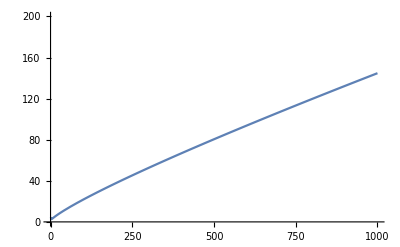

```mathematica
Plot[n/Log[n],{n,0,1000},PlotRange-> {0,200}]
```

Let’s now compare Gauss’ first approximation model with the actual PrimePi function.

Make a plot of and PrimePi[N] and N/Log[N]:

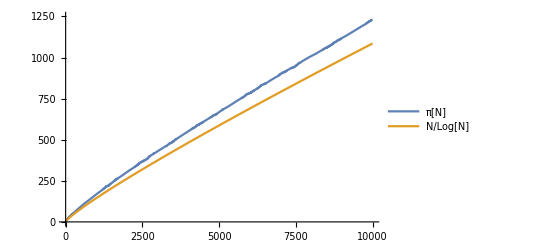

```mathematica
Plot[{PrimePi[n],n/Log[n]},{n,0,10000},PlotRange-> {0,1250},PlotLegends ->  {"π[N]","N/Log[N]"}]
```

Make a plot of absolute error of the approximation model N/Log[N]:

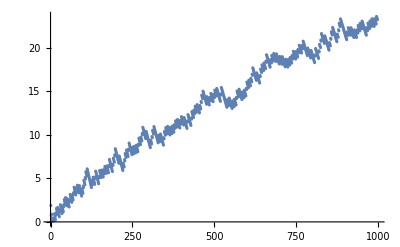

```mathematica
ListPlot[Table[Abs[(PrimePi[n]-n/Log[n])],{n,2,1000}]]
```

Make a plot of relative error of the approximation model N/Log[N]:

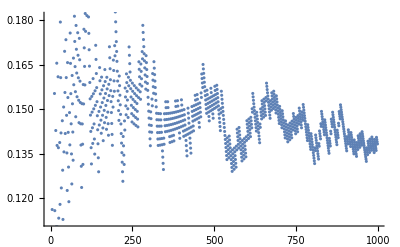

```mathematica
ListPlot[Table[Abs[(PrimePi[n]-n/Log[n])]/PrimePi[n],{n,2,1000}]]
```

In 1850, Pafnuty Chevyshev actually showed that the differences between PrimePi[N] and N/Log[N] are within 10% (-0.10~0.10) of the value for high enough number N.

Calculate the relative error of N/Log[N] for high enough number N:

```mathematica
Round[(PrimePi[10000000]-10000000/Log[10000000])/PrimePi[10000000],0.001]
```

0.066

Such result can be applied into finding approximate value of nth prime number. Since π(N)~ N/Log[N], nth prime number can be approximately be found by nLog[n]

Make a table of values comparing nth prime number, the approximation nLog[n], and the relative error:

```mathematica
Grid[Table[{Prime[n],Round[n*Log[n],1],Abs[Prime[n]-Round[n*Log[n],0.1]]/Prime[n]},{n,{1000,1000000,1000000000}}],Alignment ->  Left]
```

7919 | 6908 | 0.127693
15485863 | 13815511 | 0.107863
22801763489 | 20723265837 | 0.0911551

## LogIntegral Function

Because there were still some gaps between the approximation N/Log[N] and the PrimePi function, Mathematicians tried to develop a better approximation model. In doing so, the integral of the function 1/Log[t]caught their attention.

Make a plot of the function 1/Log[t]:

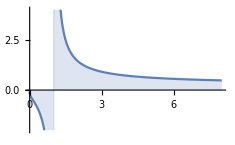

```mathematica
Plot[1/Log[t],{t,0,8},PlotRange ->  {-2,4},Filling -> Axis]
```

The area colored in the above graph is interesting in that is it greatly similar to the function N/Log[N].

Make a plot of the integral of the function 1/Log[t]:

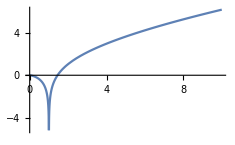

```mathematica
Plot[LogIntegral[n],{n,0,10}]
```

The above graph goes to -∞ when n is 0, becomes 0 when n is about 1.45137, and increases afterwards.

Find a value(nonzero) that makes the LogIntegral[n] 0:

```mathematica
FindRoot[LogIntegral[n]==0,{n,1.1,10}]
```

{n→1.45137}

Considering, such characteristic of the LogIntegral[N], In 1838, Peter Gustav Lejeune Diriclet conjectured that Li(N) = ∫_2^N 1/Log[t]ⅆt is a better approximation to the PrimePi function. He used 2 as lower bound because this way, the infinite value part of the function could be neglected and 1/Log[2] was small enough to be ignorant on the overall value of the function. Some people also use the value 1.45137 instead of 2 after the value has been found.

Improved Approximation model:

```mathematica
Framed["π[N]~Li[N]"]
```

π[N]~Li[N]

Let’s look at how the improved approximation model is plotted.

Make a plot of Li[n]:

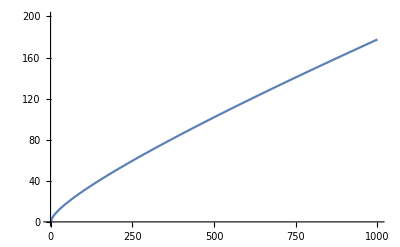

```mathematica
Plot[LogIntegral[n],{n,0,1000},PlotRange->{0,200}]
```

Let’s now compare the improved approximation model with the first approximation model and the actual PrimePi function.

Make a plot of and PrimePi[N] , N/Log[N], and Li[N]:

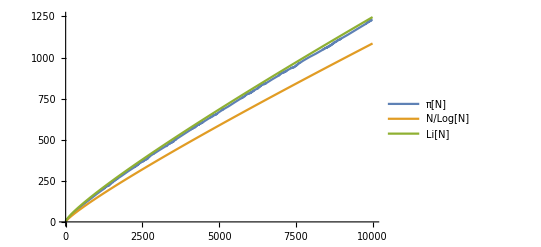

```mathematica
Plot[{PrimePi[n],n/Log[n],LogIntegral[n]},{n,0,10000},PlotRange-> {0,1250},PlotLegends->{"π[N]","N/Log[N]","Li[N]"}]
```

Make a plot of absolute error of the approximation model Li[N]:

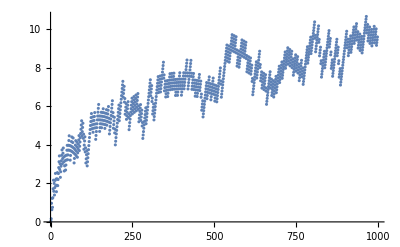

```mathematica
ListPlot[Table[Abs[(PrimePi[n]-LogIntegral[n])],{n,2,1000}]]
```

Make a plot of relative error of the approximation model Li[N]:

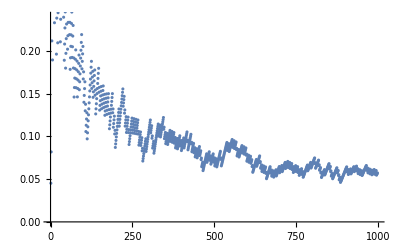

```mathematica
ListPlot[Table[Abs[(PrimePi[n]-LogIntegral[n])]/PrimePi[n],{n,2,1000}]]
```

Compare the plot of relative error between N/Log[N] and Li[N]:

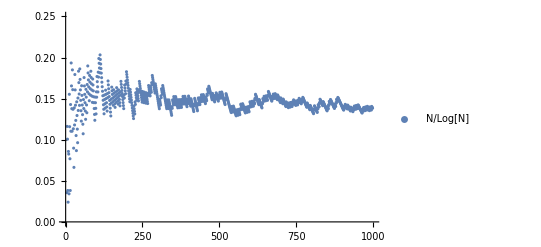
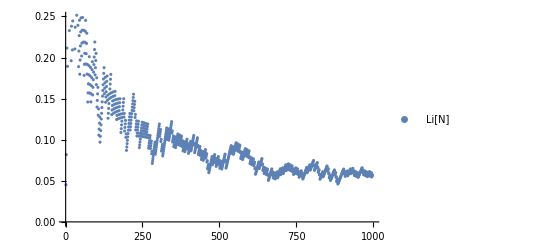

```mathematica
{ListPlot[Table[Abs[(PrimePi[n]-n/Log[n])]/PrimePi[n],{n,2,1000}],PlotRange->{0,0.25}, PlotLegends-> Placed[{"N/Log[N]"},Above]],ListPlot[Table[Abs[(PrimePi[n]-LogIntegral[n])]/PrimePi[n],{n,2,1000}],PlotRange->{0,0.25}, PlotLegends-> Placed[{"Li[N]"},Above]]}
```

## Further Improvements

Although Li[N] is a very strong approximation model for the PrimePi function, mathematicians consistently tried to make even better models for the PrimePi function. One of the examples is the usage of asymptotic expansion in Li[N].

Refined Approximation model using asymptotic expansion:

```mathematica
Framed["π[N]~N/LogN∑_(k = 0)^∞ (k!)/(Log[N])^k"]
```

π[N]~N/LogN∑_(k = 0)^∞ (k!)/(Log[N])^k

Let’s look at how the approximation model using asymptotic expansion is plotted.

Make a plot of N/LogN∑_(k=0)^∞ (k!)/(Log[N])^k. For convenience, just take the first 4 elements of the function:

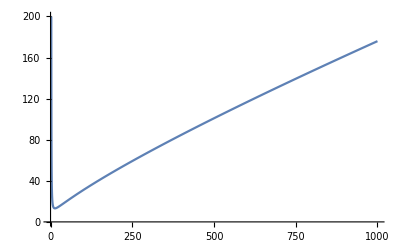

```mathematica
Plot[{Sum[Factorial[k]*n/(Log[n])^(k+1),{k,0,4}]},{n,0,1000},PlotRange-> {0,200}]
```

Let’s now compare the approximation model using asymptotic expansion, Li[N], and the actual PrimePi function for large numbers.

Make a plot of π[N], Li[N], and N/LogN∑_(k=0)^∞ (k!)/(Log[N])^k for domain 8000~10000:

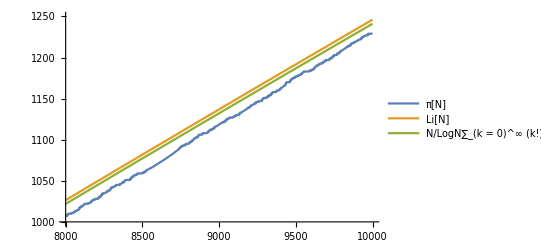

```mathematica
Plot[{PrimePi[n],LogIntegral[n],Sum[Factorial[k]*n/(Log[n])^(k+1),{k,0,4}]},{n,8000,10000},PlotRange-> {1000,1250},PlotLegends ->  {"π[N]","Li[N]","N/LogN∑_(k = 0)^∞ (k!)/(Log[N])^k"}]
```

Another refined approximation model was proposed by Riemann by subtracting small amount related with Li[N^(1/2)] from the original Li[N].

Riemann’s refined approximation model:

```mathematica
Framed["π[N]~Li[N]-1/2Li[N^(1/2)]"]
```

π[N]~Li[N]-1/2Li[N^(1/2)]

Let’s look at how Riemann’s refined approximation model is plotted.

Make a plot of Li[N]-1/2 Li[N^(1/2)]:

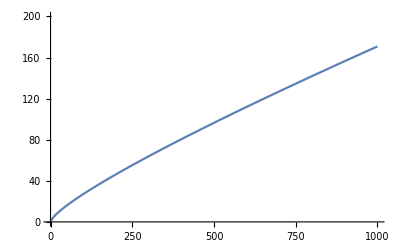

```mathematica
Plot[LogIntegral[n]-LogIntegral[n^(1/2)]/2,{n,1,1000},PlotRange->{0,200}]
```

Let’s now compare Riemann’s refined approximation model, Li[N], and the actual PrimePi function for large numbers.

Make a plot of π[N], Li[N], and Li[N]-1/2 Li[N^(1/2)]for domain 8000~10000:

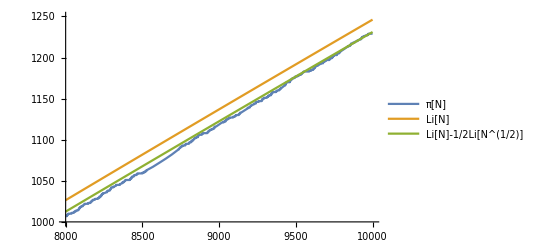

```mathematica
Plot[{PrimePi[n],LogIntegral[n],LogIntegral[n]-LogIntegral[n^(1/2)]/2},{n,8000,10000},PlotRange-> {1000,1250},PlotLegends ->  {"π[N]","Li[N]","Li[N]-1/2Li[N^(1/2)]"}]
```

With the above developments and researches related to Riemann Hypothesis, Helge von Koch finally made a model in 1901 that equates PrimePi function with a set of equations assuming that Riemann Hypothesis is true (It has still not been proven: http://mathworld.wolfram.com/RiemannHypothesis.html).

Koch’s Result:

```mathematica
"If Riemann Hypothesis is true," 
Framed["π[x]=Li[x]+O[√xLog[x]]"]
```

If Riemann Hypothesis is true,

π[x]=Li[x]+O[√xLog[x]]

Further Explorations

Investigate the relationship between PrimePi function and Riemann Hypothesis

Investigate the Big-O value for each number and make better approximation model

Authorship information

Sung Min Yoon

2017/06/23

sy375@cornell.edu